## Rosenzweig-MacArthur consumer-resource model with parasitism and a directly transmitted parasite

### Parasites increase host mortality rate

The full model assumes logistic growth of the resource (R), with a Type II functional response for both susceptible (S) and infected (Q and Q_m) hosts. We assume that all hosts are born susceptible, and that the birth rates for susceptible and infected hosts are identical. There are two strains of pathogen circulating in the population, the resident and mutant. These strains differ in their virulence (v and v_m, respectively) and transmission rates; we assume that transmission rate is a function of virulence according to β(v)=β_0 v/(1+v). 

To determine whether the mutant can invade, we need to evaluate the stability of the mutant-free equilibrium, which can do by looking at the eigenvalues of the Jacobian matrix. Notice that the Jacobian is block upper triangular, so the eigenvalues are given by the eigenvalues of the block-diagonal matrix

```mathematica
(* The model *)
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q + Qm);
dS=(es fs R)/(h+R) (S+Q + Qm)-d S-((B0 v)/(1+v)) S Q -((B0 vm)/(1+vm)) S Qm;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;
dQm=((B0 vm)/(1+vm)) S Qm-(d+vm) Qm;

(* Stability analysis *)
(* Calculate the Jacobian *)
J=Simplify[{{D[dR,R],D[dR,S],D[dR,Q], D[dR,Qm]},{D[dS,R],D[dS,S],D[dS,Q], D[dS,Qm]},
{D[dQ,R],D[dQ,S],D[dQ,Q], D[dR,Qm]},
{D[dQm,R],D[dQm,S],D[dQm,Q], D[dQm,Qm]}}]
(* Evaluate the Jacobian at the equilibrium of interest (Qm=0) *)
MatrixForm[J/.{Qm->0}]
```

{{(-fs h K (Q+Qm+S)+(K-2 R) (h+R)^2 ρ)/(K (h+R)^2),-(fs R)/(h+R),-(fs R)/(h+R),-(fs R)/(h+R)},{(es fs h (Q+Qm+S))/(h+R)^2,-d+(es fs R)/(h+R)-(B0 Q v)/(1+v)-(B0 Qm vm)/(1+vm),(es fs R)/(h+R)-(B0 S v)/(1+v),(es fs R)/(h+R)-(B0 S vm)/(1+vm)},{0,(B0 Q v)/(1+v),-d+v (-1+(B0 S)/(1+v)),-(fs R)/(h+R)},{0,(B0 Qm vm)/(1+vm),0,-d+vm (-1+(B0 S)/(1+vm))}}

((-fs h K (Q+S)+(K-2 R) (h+R)^2 ρ)/(K (h+R)^2) | -(fs R)/(h+R) | -(fs R)/(h+R) | -(fs R)/(h+R)
(es fs h (Q+S))/(h+R)^2 | -d+(es fs R)/(h+R)-(B0 Q v)/(1+v) | (es fs R)/(h+R)-(B0 S v)/(1+v) | (es fs R)/(h+R)-(B0 S vm)/(1+vm)
0 | (B0 Q v)/(1+v) | -d+v (-1+(B0 S)/(1+v)) | -(fs R)/(h+R)
0 | 0 | 0 | -d+vm (-1+(B0 S)/(1+vm)))

If the system goes to a stable equilibrium, the invasion fitness of the mutant is given by r=(β_0 v_m Ŝ)/(1+v_m)-(v_m+d), where Ŝ is the equilibrium abundance of susceptibles, set by the resident.

```mathematica
r=-d+vm (-1+(B0 S)/(1+vm));
```

#### Finding the singular strategy when the resident dynamics go to a stable equilibrium

If the resident dynamics approach the stable equilibrium, we should be able to calculate the singular strategy analytically. This will be a useful comparison point for situations where the dynamics are not stable. From the fact that, at equilibrium, dQ/dt=0, we can immediately calculate that Ŝ=((1+v)(d+v))/(β_0 v).

```mathematica
(* Calculating the equilibrium *)
Solve[dQ==0,S]
r=r/.Solve[dQ==0,S][[1]]
```

{{S→((1+v) (d+v))/(B0 v)}}

-d+vm (-1+((1+v) (d+v))/(v (1+vm)))

Thus, the invasion exponent is r=(β_0 v_m)/(1+v_m)((1+v)(d+v))/(β_0 v)-(v_m+d)=v_m/v (1+v)/(1+v_m) (d+v)-(d+v_m).
To find the singular strategy, we need to find the root of (∂r)/(∂v_m)|_(v_m=v) by calculating the derivative, setting the resulting expression equal to 0, and solving for v. From this, you can see that the singular value of v is v=√d.

```mathematica
Simplify[D[r,vm]/.{vm->v}]
```

(d-v^2)/(v+v^2)

```mathematica
Solve[Simplify[D[r,vm]/.{vm->v}]==0,v]
```

{{v→-√d},{v→√d}}

To determine whether this is an ESS, we need to look at whether the derivative (∂^2 r)/(∂v_m^2)|_(v_m=v)≤ 0. You can see that this holds for all values of v and d.

```mathematica
Simplify[D[-d+vm (-1+(B0 S)/(1+vm))/.S->((1+v) (d+v))/(B0 v),{vm,2}]/.{vm->v}]
```

-(2 (d+v))/(v (1+v)^2)

To determine whether this is an CSS, we need to look at whether the derivative d/dv((∂r)/(∂v_m)|_(v_m=v))<0. You can see that this holds for all values of v and d.

Thus, if the dynamics go to an equilibrium, there is one singular strategy that is both evolutionarily and convergence stable. You can also see that there is no dependence of the singular strategy or the fitness gradient on host resources, indicating that changes in resources will have no effect when the system is stable. It seems plausible that resources will have no effect when the dynamics are unstable, though that remains to be seen. If that is the case, then you might expect the ESS to be fairly similar in both stable and unstable populations, so whether the parasite will stabilize the host dynamics or not depends on how close the resident-only system is to the stability boundary. If the system is just barely unstable in the absence of any parasitism, then the addition of parasites will tend to stabilize.

### Calculating the invasion exponent

In general, whether a mutant can invade or not depends on the traits (parameters) of the resident. This dependence is “felt” through the effect of the resident on the dynamics of the system. 

From the above calculations, we know that whether the mutant parasite “strain” can invade or not depends on the abundance of susceptible hosts, which is determined by the traits of the resident parasite strain. To determine whether the mutant can invade, then, we need to determine the dynamics of the susceptible host population. 

If the susceptible host population goes to an equilibrium, then we can simply plug this equilibrium into the invasion exponent expression. If the host population cycles, on the other hand, then we need to calculate the average host abundance over the cycle, 1/T(∫_0)^T S(t) dt. 

For now, the only two parameters we are interested in varying are the resource carrying capacity (K) and the virulence of the resident parasite (v), so we write a new function, ‘CalcAvgS,’ that takes those two parameters as arguments, along with a parameter ‘dt’ that determines how accurate our Riemann sum approximation of the integral will be. 

First, let’s confirm that we can get different dynamics by varying the resource carrying capacity.

With K=1, the system approaches a stable equilibrium:

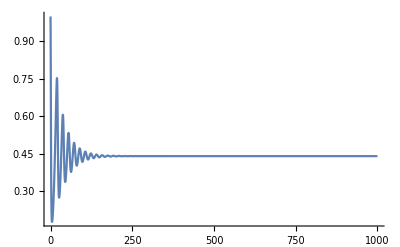

```mathematica
params={K->1,v->1,ρ->1,fs->1,h->1,d->0.1,v->0.1,B0->5,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
Plot[S[t]/.soln, {t, 0, 1000},PlotRange->All]
```

With K=2, the system cycles:

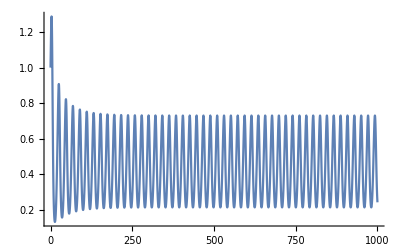

```mathematica
params={K->2,ρ->1,fs->1,h->1,d->0.1,v->0.1,B0->5,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
Plot[S[t]/.soln, {t, 0, 1000},PlotRange->All]
```

The boundary between stability and cycles when K = 2 can be found by playing around with values of d and v.

```mathematica
(* Fitness gradient *)
```

#### Using the secant method to find the singular strategies

```mathematica
fitGrad[{thisK_,thisv_,thisB0_,dt_}]:=Module[{params,K,v,ρ,fs,h,d,B0,es,dR,R,S,Q,dS,dQ,Eq,EndEq,AvgS,soln,St,FirstPeak,T,SecondPeak,Ssum},
params={K->thisK,v->thisv,ρ->1,fs->1,h->1,d->0.1,B0->thisB0,es->0.5};
dR=ρ R (1-R/K)-(fs R)/(h+R) (S+Q);
dS=(es fs R)/(h+R) (S+Q)-d S-((B0 v)/(1+v)) S Q;
dQ=((B0 v)/(1+v)) S Q-(d+v) Q;

(* Calculate the equilibria of the system *)
Eq=Solve[{dR==0,dS==0,dQ==0},{R,S,Q}]/.params;
(* Which equilibrium represents the endemic equilibrium with all values positive? *)
EndEq=Eq⟦Position[Table[AllTrue[Eq⟦i,;;,2⟧,#>0&],{i,1,Length[Eq]}],True]⟦1,1⟧⟧;
(* Does the Jacobian evaluated at this equilibrium have all negative eigenvalues e.g. is the equilibrium stable? *)
AvgS=If[AllTrue[Re[Eigenvalues[{{D[dR,R],D[dR,S],D[dR,Q]},{D[dS,R],D[dS,S],D[dS,Q]},{D[dQ,R],D[dQ,S],D[dQ,Q]}}/.params/.EndEq]],#<0&],
(* if all e-values are negative, return the equilibrium S *)
EndEq⟦2,2⟧,
(* otherwise, numerically solve *)
soln=NDSolve[{S'[t]==(dS/.{S->S[t],Q->Q[t],R->R[t]}),Q'[t]==(dQ/.{S->S[t],Q->Q[t],R->R[t]}),R'[t]==(dR/.{S->S[t],Q->Q[t],R->R[t]}),S[0]==1,Q[0]==0.1,R[0]==K/2}/.params,{S,Q,R},{t,0,1000},AccuracyGoal->Infinity, PrecisionGoal->10];
St=Table[(S[t]/.soln)⟦1⟧,{t,800,900,dt}];
(* find the first peak of the cycle *)	
FirstPeak= 800+Position[St,Max[St]]⟦1,1⟧ dt;
(* Find next peak *)
St=Table[(S[t]/.soln)⟦1⟧,{t,FirstPeak,1000,dt}];
(* Cycle period *)
T=Position[Table[(St⟦t⟧-St⟦t+1⟧)/(St⟦t+1⟧-St⟦t+2⟧),{t,1,Length[St]-2}],_?(#<0&)]⟦2,1⟧ dt;
(* Next peak *)
SecondPeak=FirstPeak+T;
(* Riemann sum to find the integral of S(t) over the cycle *)
Ssum=Sum[dt (S[t]/.soln)⟦1⟧,{t,FirstPeak+dt/2,SecondPeak+dt/2,dt}];
(* calculate the average S *)
Ssum/T
];
Abs[(B0 AvgS-(1+v)^2)/(1+v)^2/.params]
];
```

A better way to do it will be to write a custom root finding algorithm. We can do this using the secant method, which is essentially a finite difference approximation of Newton’s method, since we cannot compute the derivative of the fitness gradient with respect to v. To use this method, you must provide two initial values for v, and then you converge from there using the recursion relation v_n=(v_(n-2)f(v_(n-1))-v_(n-1)f(v_(n-2)))/(f(v_(n-1))-f(v_(n-2))).

```mathematica
calcvBounds[{Kval_,B0val_}]:=Module[{ρ,K,fs,h,es,d,B0,v,params,bounds},
params={K->Kval,ρ->1,fs->1,h->1,d->0.1,B0->B0val,es->0.5};
(* Figure out when the per-capita growth rate of the infectious class is equal to zero, when the susceptible population is at its maximum *)
bounds=Solve[(B0 v)/(1+v)((es h (-d h-d K+es fs K) ρ)/((d-es fs)^2 K))-d-v==0,v]/.params;
{Min[bounds[[;;,1,2]]],Max[bounds[[;;,1,2]]]}
]
```

```mathematica
secantMethod[{v0init_,v1init_,Kval_,B0val_,convcrit_}]:=Module[{v0uncon,v1uncon,v0con,v1con,conv,g0,g1,v2con,v2uncon,vbnds},
(* set the unconstrained v values for use in calculating the fitness gradient *)
v0uncon=v0init;
v1uncon=v1init;
(* calculate the bounds on v *)
vbnds=calcvBounds[{Kval,B0val}];
(* convert v to the unconstrained scale for use in the recurrence relation *)
v0con=Log[((v0uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v0uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
v1con=Log[((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
(* Set the initial value of the convergence measure *)
conv=1;
While[conv>convcrit,
(* compute the value of the fitness gradient at the unconstrained values of v0 and v1 *)
g0=fitGrad[{Kval,v0uncon,B0val,0.001}];
g1=fitGrad[{Kval,v1uncon,B0val,0.001}];
(* use the recurrence relation to update the constrained value of v *)
v2con=(v0con g1-v1con g0)/(g1-g0);
(* compute the unconstrained version *)
v2uncon=Exp[v2con]/(1+Exp[v2con]) (Max[vbnds]-Min[vbnds])+Min[vbnds];
v2uncon=If[v2uncon==Min[vbnds],Min[vbnds]+0.0001,v2uncon];
v2uncon=If[v2uncon==Max[vbnds],Max[vbnds]-0.0001,v2uncon];
(* set the convergence criterion to the lower of g1 and g2 *)
conv=Min[{Abs[g0],Abs[g1]}];
(* update the unconstrained and constrained values of v0 and v1 *)
v0uncon=v1uncon;
v0con=v1con;
v1uncon=v2uncon;
v1con=Log[((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds]))/(1-((v1uncon-Min[vbnds])/(Max[vbnds]-Min[vbnds])))];
];
v2uncon
]
```

The value I would expect is v=√d=√0.1=0.316228.

```mathematica
Sqrt[0.1]
```

This is exactly what I see for K=1, which produces a stable equilibrium.

```mathematica
secantMethod[{0.1,0.11,1,5,10^-12}]
```

0.316228

But it is also what I get when K=2, which produces a stable limit cycle.

```mathematica
secantMethod[{0.1,0.11,2,5,10^-12}]
```

0.316228

Thus, if no aspect of virulence, transmission, or host background mortality depends on resources, resources will have no effect on the evolution of virulence.